## Example 10.3

```mathematica
Clear["Global`*"]
```

```mathematica
SetOptions[Plot,Axes->False,Frame->True,BaseStyle->{FontSize->16}];
```

```mathematica
H=100;
w=7.272*10^(-5);  (* angular velocity of Earth *)
g = 9.8;
```

```mathematica
Deflection[λ_]:=1/3*w*Sqrt[8*H^3/g]*Cos[λ * π/180];
```

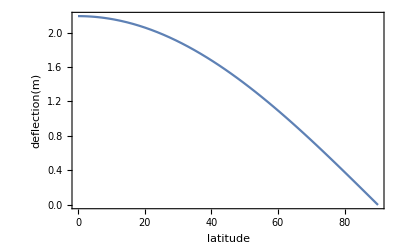

```mathematica
Plot[100*Deflection[λ],{λ,0,90},FrameLabel->{"latitude","deflection(m)"}]
```

## Example 10.4

```mathematica
Clear["Global`*"]
```

```mathematica
SetOptions[ParametricPlot,Frame->True,BaseStyle->{FontSize->16}];
```

```mathematica
l=67;
λ=48.8*Pi/180;
g=9.8;
w=7.727*10^(-5);
wz=w*Sin[λ];
β=g/l;
```

```mathematica
soln=NDSolve[{x''[t]+ β^2*x[t]== 2*wz*y'[t],
y''[t]+β^2*y[t]==-2*wz*x'[t],
x[0]==0.1,y[0]==0,x'[0]==0,y'[0]==0},{x[t],y[t]},{t,0,27000}];
```

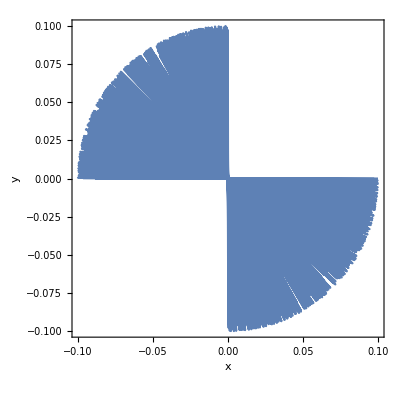

```mathematica
ParametricPlot[{x[t],y[t]}/.soln,{t,0,27000},FrameLabel->{"x","y"}]
```

## Example 10.5

```mathematica
Clear["Global`*"]
```

```mathematica
ω=7.272 10^(-5);
α=45*Pi/180;
λ=50*Pi/180;
v0=200;
g=9.8;
```

```mathematica
z0Dot=v0 Sin[α];
y0Dot=v0 Cos[α];
```

```mathematica
soln=NDSolve[{x''[t]==2y'[t]ω Sin[λ],y''[t]==-2z'[t]ω Cos[λ]-2x'[t]ω Sin[λ],z''[t]==-g+2y'[t]ω Cos[λ],x'[0]==0,y'[0]==y0Dot,z'[0]==z0Dot,x[0]==0,y[0]==0,z[0]==0},{x,y,z},{t,0,2000}];
```

```mathematica
T=FindRoot[(z[t]/.soln)==0,{t,10,2000}][[1,2]]
```

28.9005

```mathematica
x[T]/.soln[[1]]
```

6.57713

```mathematica
y[T]/.soln[[1]]
```

4085.3